## Numeric Solution

```mathematica
f={X,Y,Z}/.NDSolve[{
X'[t]==-(Y[t]+Z[t]),
Y'[t]==X[t]+a Y[t],
Z'[t]==b+X[t]Z[t]-c Z[t],
X[0]==1,Y[0]==1,Z[0]==1}/.{a->.2,b->.2,c->8},
{X,Y,Z},{t,0,50}][[1]]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

## Plots solutions along each axis

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

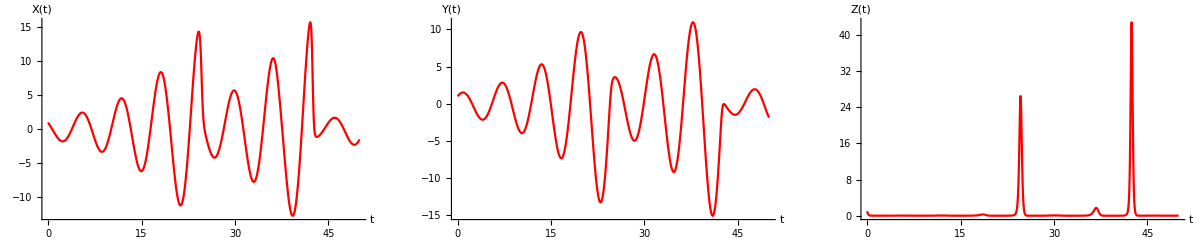

```mathematica
l={X[t],Y[t],Z[t]};
Show[GraphicsArray[Table[Plot[f[[i]][t],{t,0,50},PlotRange->All,
PlotStyle->Red,
AxesLabel->TraditionalForm/@{t,l[[i]]},DisplayFunction->Identity],{i,3}]
]]
```

### Attractor

```mathematica
s=NDSolve[{Derivative[1][x][t]==-3 (x[t]-y[t]),Derivative[1][y][t]==-x[t] z[t]+26.5 x[t]-y[t],Derivative[1][z][t]==x[t] y[t]-z[t],x[0]==z[0]==0,y[0]==1},{x,y,z},{t,0,400},MaxSteps->∞];
```

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.s],{t,0,400},PlotPoints->1000,PlotRange->All,PlotStyle->Directive[Thick,RGBColor[.8,0,0]],ColorFunction->(ColorData["SolarColors",#4]&)]
```

-Graphics3D-